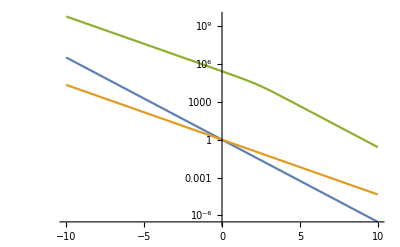

```mathematica
LogPlot[{Exp[-3/2t],Exp[-t],Abs[Exp[-3/2t]BesselJ[10 I,100Exp[-t]]]},{t,-10,10}]
```

```mathematica
?BesselJ
```

BesselJ[n,z] gives the Bessel function of the first kind J_n(z).

```mathematica
Integrate[]
```

```mathematica
F[z_]:=Sin[z];
NewtonRaphsonStep[z_]:=z-F[z]/F'[z]
```

```mathematica
ls=Round[FixedPoint[NewtonRaphsonStep,#]/Pi&/@Table[i+j I,{j,-.5,.5,0.011/4},{i,Pi/2.-.5,Pi/2.+.5,0.011/4}]];
```

```mathematica
ListDensityPlot[1+Tanh[ls/2.],ColorFunction->"Rainbow"]
```

-Graphics-

-Graphics-

```mathematica
ArcTan[x]/Tanh[x]
```

ArcTan[x] Coth[x]

```mathematica
ls//Dimensions
```

{364,364}

```mathematica
ls[[50,190]]
```

11

```mathematica
ls[[50]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-2,-3,-3,-3,-3,-3,-3,-3,-4,-4,-4,-4,-5,-5,-5,-6,-6,-7,-7,-8,-9,-10,-12,-13,-16,-18,-18,-12,4,16,19,18,16,14,12,11,10,9,8,7,7,5,6,6,5,5,5,5,4,4,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Sin[I z]
```

ⅈ Sinh[z]

```mathematica
1
```

```mathematica
2-Pi/2.
```

0.429204